# Aggregation Systems

Kabir Khanna

Christopher Wolfram and Jonathan Gorard

# Introduction

Aggregation Systems are a stochastic analog to the Cellular Automaton.  Unlike Cellular Automaton, where every step is deterministic and it grows one row at a time , Aggregation Systems grow by adding one cell at a time at randomly chosen locations. But at the same time, there are certain underlying rules similar to the Cellular Automaton rules they follow. For example,

```mathematica
-Graphics-->-Graphics-                                                                                                   -Graphics-->-Graphics-
```

As you can see, the Aggregation System model basically follows the rules of the Cellular Automaton but instead of adding all the cells in the following row, it picks one at random. After around 30 steps, this is how they both look (Rule 30 of elementary Cellular Automaton).

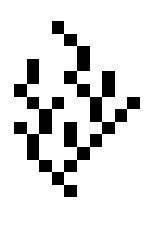
```mathematica
-Graphics-                                                                                -Graphics-
```

A lot of “random” behaviour of nature could be modelled using the Outer Totalistic and Totalistic Rule Set of the Aggregation System and hence, most of the results in the following notebook are calculated for the Outer Totalistic Case (2D) with an initial condition of an array with one black cell at the center.

# The Aggregation System function

The first step was to write up a function which took in similar arguments as the Cellular Automaton and gave the Aggregation System as the output corresponding to the given rule.

```mathematica
Clear[framedAggregationSystem];
framedAggregationSystem[rule_, init_, steps_]:= Catch[Module[{r, p, pos, output1},Nest[
(
r=CellularAutomaton[rule,#];
pos= Position[r, Except[0], {Depth[init]-1}, Heads->False];
If[pos=== {}, Throw[#]];
p=RandomChoice@pos;
output1 = ReplacePart[#,p-> Extract[r, p]]
)&,init,steps]]]
```

```mathematica
ArrayPlot@framedAggregationSystem[<| "OuterTotalisticCode"-> 30 , "Dimension"-> 2|>, CenterArray[1, {50,50}], 200]
```

-Graphics-

But this algorithm is inefficient because we need to define an arbitrary size of the frame to fit the Aggregation System and the algorithm goes on evaluating the white background cells even when the Aggregation System dies down. The next step was to overcome this issue. For that, I evaluated each step of the Aggregation System and evolved the frame accordingly along with the frame.

```mathematica
unpad[a_]:=(ReplacePart[a,Thread[(Replace[#,All->_,1]&/@Select[Catenate@Table[Append[ConstantArray[All,n],m],{n,0,Depth[a]-2},{m,{1,-1}}],AllTrue[Flatten[Extract[a,#]],#===0&]&])->Nothing]])
Clear[AggregationSystem];
AggregationSystem[rule_, init_, steps_]:= Catch[Module[{r, p, pos, output1,output2,cent=0},Nest[
(output1=ArrayPad[#,1];
cent+=1;
r=CellularAutomaton[rule,output1];
pos= Position[r, Except[0], {Depth[init]-1}, Heads->False];
If[pos=== {}, Throw[#]];
p=RandomChoice@pos;
output1 =output2= ReplacePart[output1,p-> Extract[r, p]];
output1=unpad[output1];
(*Print[{output1, output2}]//MatrixForm;*)
(*Print[Dimensions/@{output1,output2}];*)
(*If [Dimensions[output1]===(Dimensions[output2]-{2,2}),cent=cent-1]*);
output1
)&,init,steps]]]
```

```mathematica
ArrayPlot@AggregationSystem[<| "OuterTotalisticCode"-> 30 , "Dimension"-> 2|>, CenterArray[1, {1,1}], 200]
```

-Graphics-

This made the performance significantly better. Time vs Iterations:

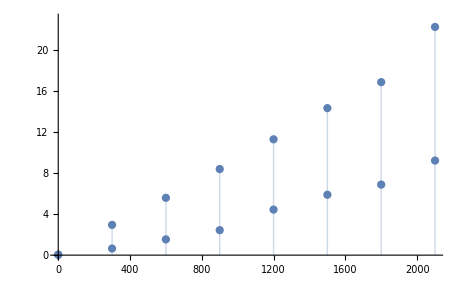

# Overview of the rules

One of the brute force ways to get some intuition and understanding about which directions to look for, is to simply run all the rules and stare at them:

```mathematica
-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-
```

This set is the visual of the valid Aggregation System rules until 1510 (each for 200 iterations). If you look carefully, you’ll notice that a few rules have been skipped. This is because they’re either uninteresting (flicker) or do not grow at all given the Center Array initial condition. The rules might grow given other initial condition but in this current project, only the Center Array initial condition was studied since it’s a reasonable place to start.

# Tests and Experiments

#### Dimensions

If one stares at the rules for a while, you realise that there is some sort of burst in the dimensions after a certain discrete rule number. This hints towards behaviour during systems where there is a phase change of some sort. For example, rule 510 →516:

```mathematica
-Graphics-                                                                                                  -Graphics-
```

Just to be sure that this wasn’t happening by chance, I iterated rule 510 and 516 20 times and plotted out their dimension.

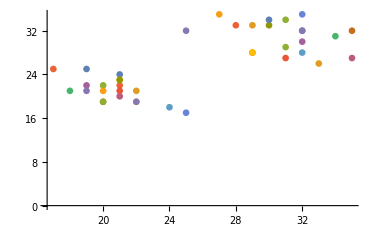

```mathematica
ListPlot[Table[( Dimensions@AggregationSystem[<|"OuterTotalisticCode"-> #, "Dimension"-> 2|>, CenterArray[1, {1,1}], 200]&/@{510, 516}), {n, 1, 20}]]
```

As one can see, this is a characteristic of the Aggregation Systems and not something that was happening by chance. If one thinks about it, it is not coming from nowhere. A glance at the rule plots for both the rules gives us a better idea

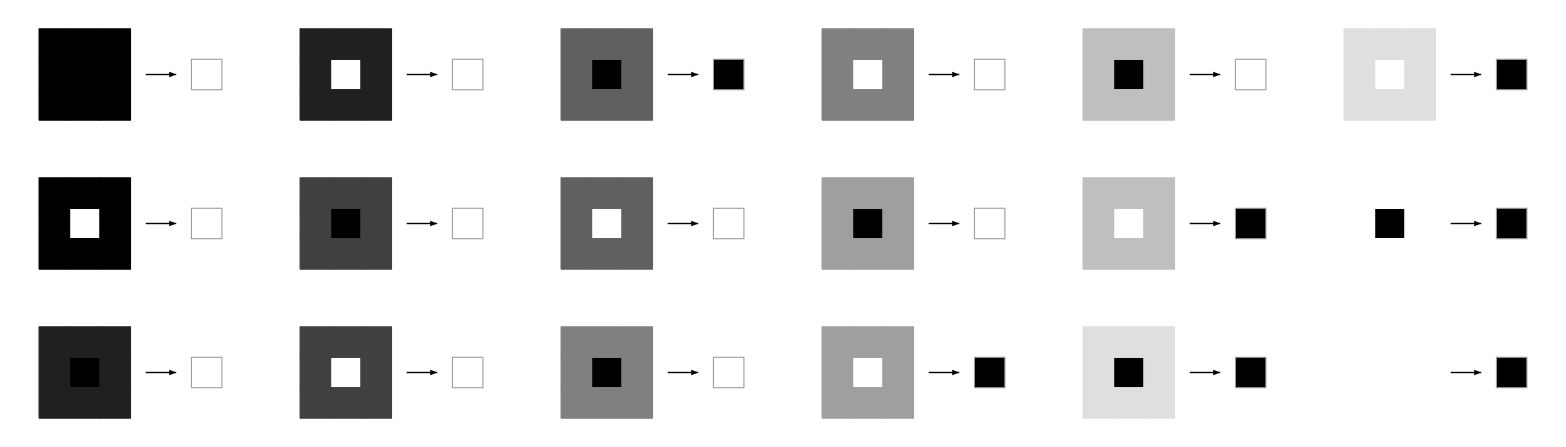
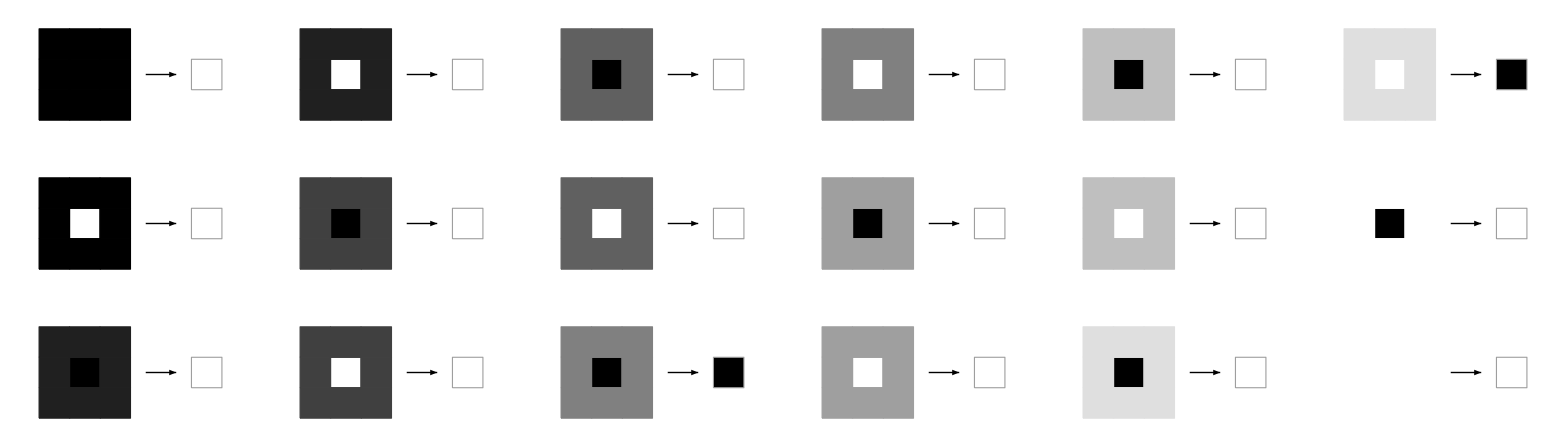

```mathematica
RulePlot[CellularAutomaton[<|"OuterTotalisticCode"-> #, "Dimension"-> 2|>]]&/@{2143, 516}
```

Rule 510 has more chances of turning the subsequent cells black than 516. This explains why rule 510 is more denser and packed compared to rule 516. This discrete jump in dimension happens as we cross powers of two.

If we pick the first 1000 “valid” set of rules and plot their dimensions (Distance from origin), we get the following “noisy” graph with peaks at places. These peaks mostly occur at around the powers of 2 for reasons explained above.

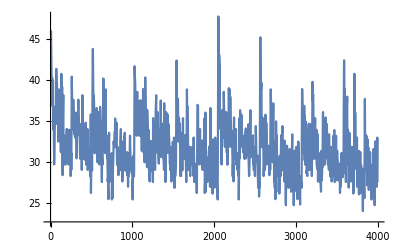

### Probabilistic measures: Standard deviation

On iterating each rule a several number of times, we get a different picture almost every time as the cells are picked one at a time from a set of a finite possible options. This raises a question of whether there exists some sort of a typical behavior characteristic to a rule we can predict before hand given the rule number. One of the measures to look at it is the Standard Deviation of the pixel values {0,1} after iterating a rule for a fixed number of iterations.

```mathematica
available = available = Select[Range[2^18-1],EvenQ[#] &&!IntegerQ[#/8]&&!IntegerQ[(#-10)/8]&];
stdeviationrandomavailable[iterations_, n_]:=
( a = RandomSample[available, n];
KeyValueMap[N@StandardDeviation@#2&,Merge[Table[AssociationMap[AggregationSystem[<| "OuterTotalisticCode"-> # , "Dimension"-> 2|>, CenterArray[1, {50,50}], 500]&, a], {k,iterations}],Identity]]
)
AssociationThread[a, ArrayPlot/@stdeviationrandomavailable[10, 5]]
```

StandardDeviation::rectt: Rectangular array expected at position 1 in StandardDeviation[{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«47»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»}}].

StandardDeviation::rectt: Rectangular array expected at position 1 in StandardDeviation[{«1»}].

ArrayPlot::mat: Argument StandardDeviation[{«1»}] at position 1 is not a list of lists.

<|a→ArrayPlot[StandardDeviation[{1}]]|>
 |  |  |  |

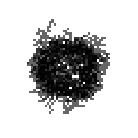
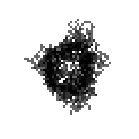
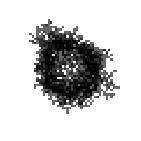
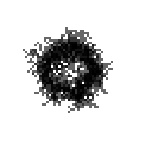
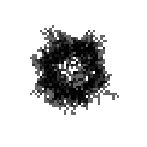
```mathematica
<|110324->-Graphics-,205492->-Graphics-,224140->-Graphics-,27388->-Graphics-,9956->-Graphics-|>
```

Doing it for more number of iterations, the picture becomes more clear.

We notice that many of the rules have a dark halo at the edges. This happens because when we run a rule multiple number of times, the inner section almost remains the same; like a dense blob. Only at the outer parts of the system that there is uncertainty of the positions of the cells leading to a higher standard deviation. But this is not always true as one would normally expect. For example,

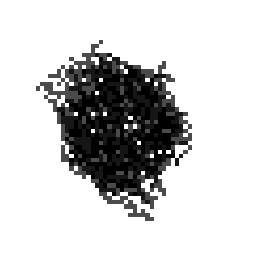
```mathematica
2143->-Graphics-
```

In this case, there is uncertainty engraved in the rule from the very beginning and the standard deviation plot almost looks like a black blob. If we go on to plot something analogous to the moment of inertia in that case of these Standard deviation visuals (vs Rule Number), we get an idea as to what is the distribution of the two types of Standard Deviation representations.

```mathematica
datastdev = Import["stdeviationdata.mx"];
ListPlot@AssociationThread[labels, Table[N[Total[Flatten@MapIndexed[#1*(EuclideanDistance[Dimensions[datastdev[[n]]]/2,#2]^2)&,datastdev[[n]],{2}]]], {n, 1, 3000}]]
```

$Aborted

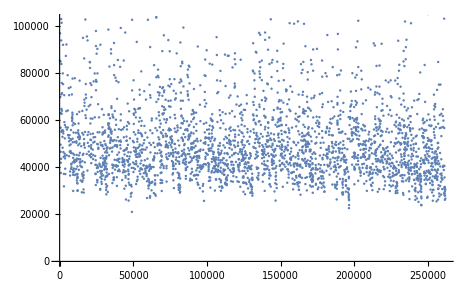

```mathematica
Histogram[AssociationThread[labels, Table[N[Total[Flatten@MapIndexed[#1*(EuclideanDistance[Dimensions[datastdev[[n]]]/2,#2]^2)&,datastdev[[n]],{2}]]], {n, 1, 3000}]]]
```

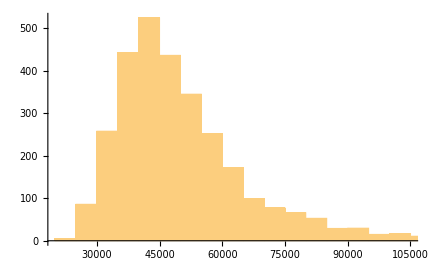

```mathematica
FindDistribution[Table[N[Total[Flatten@MapIndexed[#1*(EuclideanDistance[Dimensions[datastdev[[n]]]/2,#2]^2)&,datastdev[[n]],{2}]]], {n, 1, 3000}]]
```

```mathematica
MixtureDistribution[{0.9262480618395671,0.07375193816043307},{LogNormalDistribution[10.709938521692017,0.24927531644683798],LogNormalDistribution[11.375808011619768,0.3116990014250025]}]
```

### Mean

Another thing that comes to mind after Standard deviation is the mean of the rules after iterating multiple times.

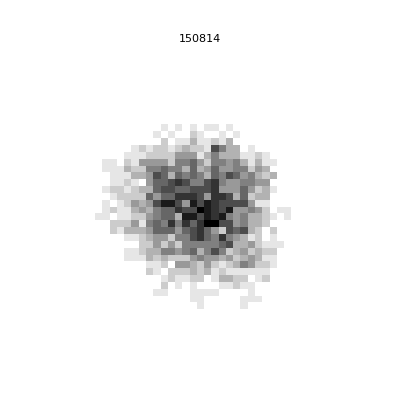
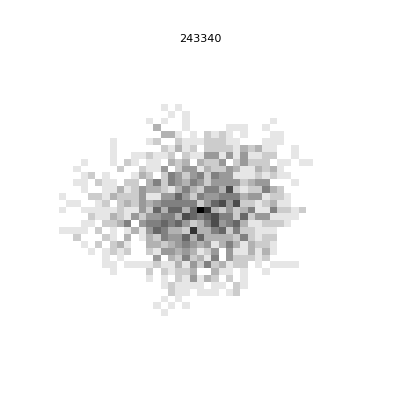
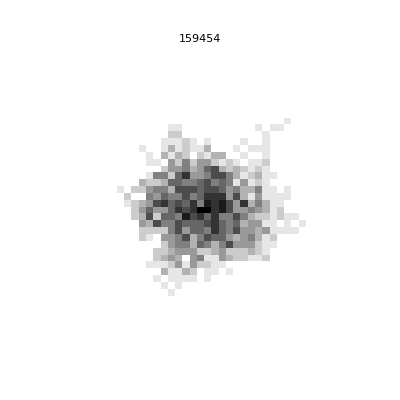
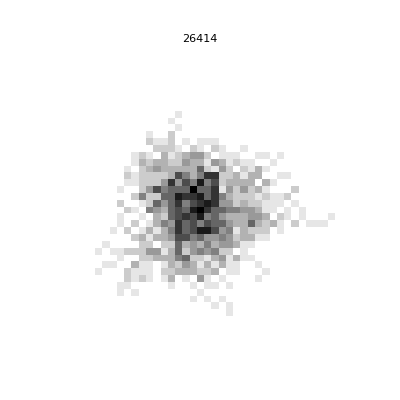
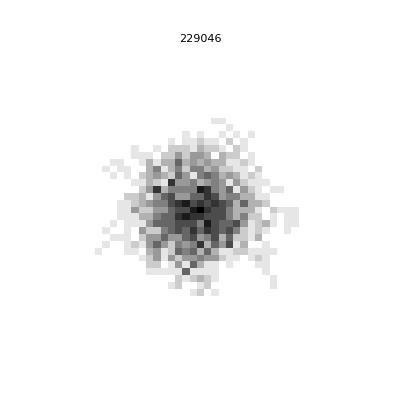
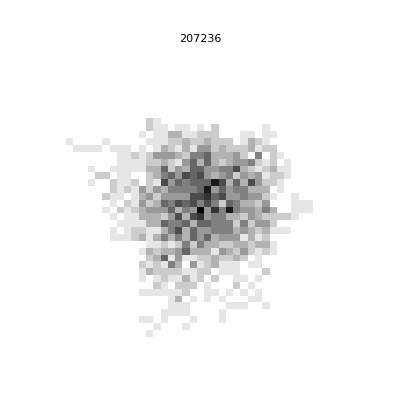
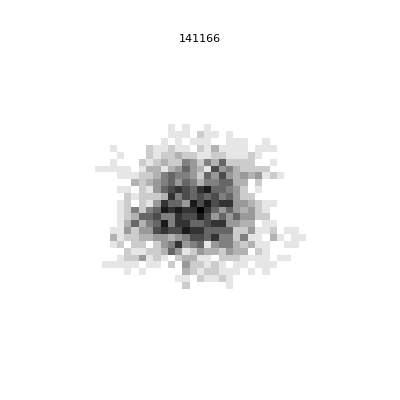
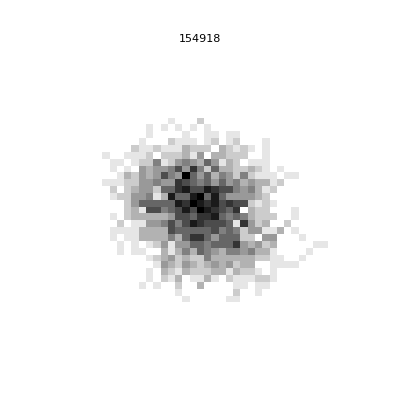

```mathematica
meanrandomavailable[n_, iterations_]:=
(a = RandomSample[available, n];
KeyValueMap[ArrayPlot[N@Mean@#2, PlotLabel-> #1]&,Merge[Table[AssociationMap[AggregationSystem[<| "OuterTotalisticCode"-> # , "Dimension"-> 2|>, CenterArray[1, {45,45}], 200]&,a], {k,iterations}],Identity]])
meanrandomavailable[10,10]
```

This again tells us about the characteristic of rules. Certain rules like 159454 have a Gaussian distribution implying that they’re more likely to land in that particular spot than in other places. On the other hand, some rules like 193062 is roughly of the same probability everywhere implying that a cell is equally likely to land in any given area. They display a dispersed behaviour in comparison to the rules like 159454.

## Confluence: An exploration

Confluence is essentially a property of a rewrite system which indicates whether or not a system (observed) can be transformed or rewritten in a way that the input of an abstract rewrite pair overlaps  to the same result after the following iteration. If this happens over a single rewrite rule iteration for all given states of a system, the system is said to be locally or weakly confluent and the system is said to display the Church-Rosser property. If this, occurs over multiple transformation steps, the system is said to be globally confluent. 
Confluence is usually studied in deterministic systems and study of confluence hasn’t really been taken up in stochastic systems. Here, I aim to bring up an idea of confluence in the case of these stochastic Aggregation Systems.

### “Theoretical” Confluence (weak) in Aggregation Systems:

Given an initial condition of the Center Array and a rule, there are different states in which a system can evolve to. Some of these states can be further evolved to converge into the same state. For example,

```mathematica
Clear[DeterministicAggregationSystem];
DeterministicAggregationSystem[rule_, init_]:= Catch[Module[{r, pos},Nest[
(
r=CellularAutomaton[rule,#];
pos= Position[r, Except[0], {Depth[init]-1}, Heads->False]; 
If[pos=== {}, Throw[#]];

Function[p,ReplacePart[#,p-> Extract[r, p]]]/@pos
)&,init,1]]
]
```

The above function gives the list of all the immediate possible states given an initial condition.

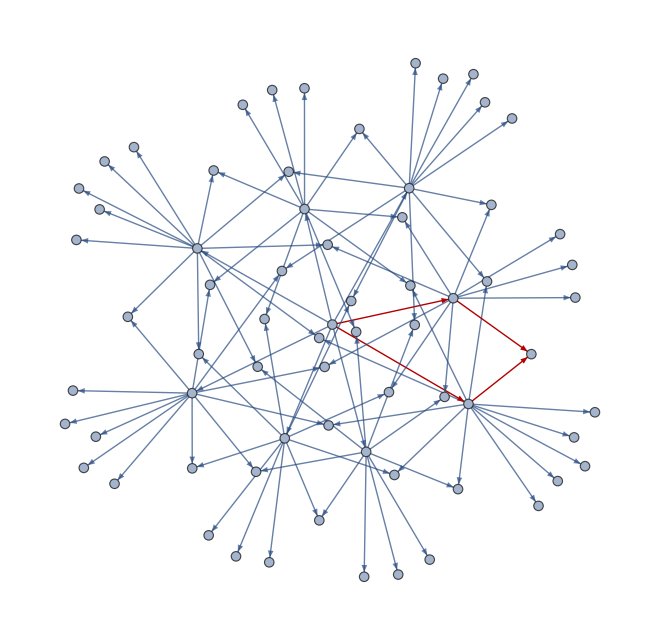

```mathematica
removeSelfLoops[g_Graph]:=Graph[DeleteCases[EdgeList[g],(DirectedEdge|UndirectedEdge)[x_,y_]/;x===y],Sequence@@Options[g]]
theoreticalconfluencegraph2[rule_,iters_,initI_:CenterArray[1,{5,5}]]:=Module[{graphint},
graphint = Graph[Labeled[#,#,Center]&/@VertexList[#],DeleteDuplicates@EdgeList[#]]&@Graph[
Catenate[Module[{newInit},Reap[Nest[
Catenate@*Map[Function[init,
newInit=DeterministicAggregationSystem[rule,init];
Sow[ArrayPlot[init,ImageSize->15]->ArrayPlot[#,ImageSize->15]&/@newInit];
newInit
]],
{initI},iters];
]][[2,1]]]
];
removeSelfLoops[graphint]
]
g = theoreticalconfluencegraph2[<| "OuterTotalisticCode"->30, "Dimension"-> 2 |>, 2];
g = HighlightGraph[g, {ReplacePart[VertexList[g][[{1,2}]],0->DirectedEdge]}];
g = HighlightGraph[g, {ReplacePart[VertexList[g][[{2,14}]],0->DirectedEdge]}];
g = HighlightGraph[g, {ReplacePart[VertexList[g][[{1,3}]],0->DirectedEdge]}];
g = HighlightGraph[g, {ReplacePart[VertexList[g][[{3, 14}]],0->DirectedEdge]}]
```

The highlighted part of the graph is one of the possible paths that can be taken by the system that converge after two iterations. We calculate the probability of achieving such states since these bring the confluence to the rule. For example, there is a {1/8*1/10, 1/8*1/10} chance to take those paths on multiple iterations. Then, we go on to calculate such probabilities for all such convergent states and take the sum. This, in essence, defines a theoretical confluence level of a particular rule.

```mathematica
theoreticalconfluencevalue [graph_]:= 
(Module[{val, probs},probs = Select[AssociationMap[Apply[Function[{v1,v2},Function[path,1/Times@@(VertexOutDegree[graph,#]&/@Most[path])]/@FindEdgeIndependentPaths[graph,v1,v2,Infinity]]],Permutations[VertexList[graph],{2}]],Length[#]>1&];
Print[probs];
val = N[Total@Flatten@Values@probs]
])
theoreticalconfluencevalue[g]
```

<|{-Graphics-,-Graphics-}→{1/80,1/96},{-Graphics-,-Graphics-}→{1/96,1/96},{-Graphics-,-Graphics-}→{1/80,1/96},{-Graphics-,-Graphics-}→{1/80,1/96},{-Graphics-,-Graphics-}→{1/96,1/96},{-Graphics-,-Graphics-}→{1/80,1/96},{-Graphics-,-Graphics-}→{1/96,1/96},{-Graphics-,-Graphics-}→{1/96,1/80},{-Graphics-,-Graphics-}→{1/80,1/80},{-Graphics-,-Graphics-}→{1/80,1/80},{-Graphics-,-Graphics-}→{1/96,1/80},{-Graphics-,-Graphics-}→{1/80,1/80},{-Graphics-,-Graphics-}→{1/96,1/80},{-Graphics-,-Graphics-}→{1/80,1/96},{-Graphics-,-Graphics-}→{1/80,1/96},{-Graphics-,-Graphics-}→{1/96,1/96},{-Graphics-,-Graphics-}→{1/80,1/96},{-Graphics-,-Graphics-}→{1/96,1/96},{-Graphics-,-Graphics-}→{1/80,1/80},{-Graphics-,-Graphics-}→{1/96,1/80},{-Graphics-,-Graphics-}→{1/80,1/80},{-Graphics-,-Graphics-}→{1/96,1/80},{-Graphics-,-Graphics-}→{1/96,1/80},{-Graphics-,-Graphics-}→{1/80,1/80},{-Graphics-,-Graphics-}→{1/96,1/80},{-Graphics-,-Graphics-}→{1/80,1/96},{-Graphics-,-Graphics-}→{1/96,1/96},{-Graphics-,-Graphics-}→{1/96,1/80}|>

0.641667

#### Experimental Evaluation of weak confluence

Until now, we algorithmically defined and calculated the theoretical confluence level of a given rule set. But the speculation is that this might not be so simple after all and it is a good idea to compare it to the real Aggregation System by actually running it and fetching raw data.

#### Algorithm

Given a rule set and thee initial condition of the central array, two iterations of the Aggregation Systems are evaluated for a certain sample number of times (200+) and displayed as a graph. To get the confluence level in the rule set, we first count the number of pairs of edges that point to a particular state in the second iteration from non-overlapping first iterations. We then divide this number by the total number of “VertexOut”  edges from the corresponding first iteration states. Finally, if this occurs for multiple states in the second iteration, the ratios are independently added and the resulting value is the experimental confluence level of the rule set.

```mathematica
countofpairs[g1_]:= (Module[{tallymultiple, frequencies},
tallymultiple=Select[Table[Tally@GroupBy[EdgeList[g1],#⟦2⟧&][[i]], {i, Length@GroupBy[EdgeList[g1],#⟦2⟧& ]}], Length[#]>1&];
frequencies = Table[Table[tallymultiple[[i,j,2]], {j, 1, Length[tallymultiple[[i]]]}], {i, 1, Length[tallymultiple]}];
AssociationThread[Table[tallymultiple[[i,1,1,2]], {i, 1, Length[tallymultiple]}],Table[Binomial[Total[frequencies[[i]]], 2]-Sum[Binomial[frequencies[[i,j]],2] ,{j, Length[frequencies[[i]]]} ], {i, 1, Length[frequencies]}] ]])
```

```mathematica
removeSelfLoops[g_Graph]:=Graph[DeleteCases[EdgeList[g],(DirectedEdge|UndirectedEdge)[x_,y_]/;x===y],Sequence@@Options[g]]
```

```mathematica
confluencegraph[rule_, iter_]:=(Module[{step1, step2, g, confgraph},
step1=Table[AggregationSystem[<| "OuterTotalisticCode"-> rule, "Dimension"-> 2 |>,CenterArray[1, {10, 10}], 1], {i, iter}];
step2 = Table[AggregationSystem[<| "OuterTotalisticCode"-> rule, "Dimension"-> 2 |>,step1[[i]], 1], {i, iter}];
g=Graph[Flatten[{
Thread[DirectedEdge[(ArrayPlot[#,ImageSize->20]&/@step1),(ArrayPlot[#,ImageSize->20]&/@step2)]]
}]];
confgraph = removeSelfLoops@Graph[Labeled[#,#,Center]&/@VertexList[g],EdgeList[g]]
])
```

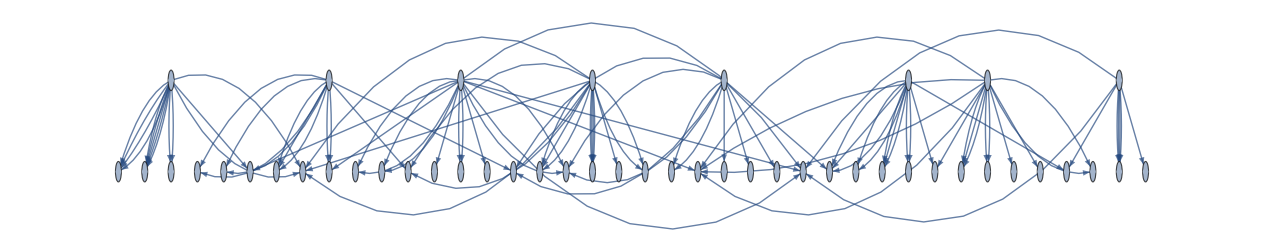

1.24847

```mathematica
confluencevalue[graph_Graph]:=Module[{keys, inOutDegree, exprob},
(keys=Keys@countofpairs[graph];
inOutDegree=AssociationMap[AssociationMap[VertexOutDegree[graph,#]&,DeleteCases[VertexInComponent[graph,#,1],#]]&,keys];
exprob=Merge[{countofpairs[graph],Total/@inOutDegree},#[[1]]/#[[2]]&];
Total[exprob])]
experimentalconfluencegraph = confluencegraph[100, 100]
confluencevalue[experimentalconfluencegraph]//N
```